```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<ggHCzakonNiggetiedt.m
```

```mathematica
LORePlot = Plot[Re[C0[z]], {z, 0.01, 4}, PlotRange->All, PlotStyle->Green];
NLORePlot = Plot[Re[C1I[z]], {z, 0.01, 4}, PlotRange->All, PlotStyle-> Blue];
NNLORePlot = Plot[Re[C2I[z, 5]]/10, {z, 0.01, 4}, PlotRange->All,PlotStyle->Red];
```

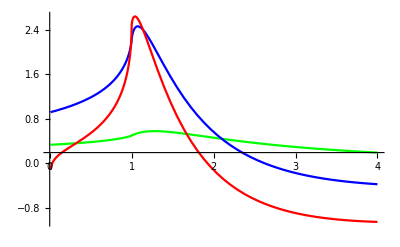

```mathematica
Show[LORePlot, NLORePlot, NNLORePlot]
```

```mathematica
LOImPlot = Plot[Im[C0[z]], {z, 0.01, 4}, PlotRange->All, PlotStyle->Green];
NLOImPlot = Plot[Im[C1I[z]], {z, 0.01, 4}, PlotRange->All, PlotStyle-> Blue];
NNLOImPlot = Plot[Im[C2I[z, 5]], {z, 0.01, 4}, PlotRange->All,PlotStyle->Red];
```

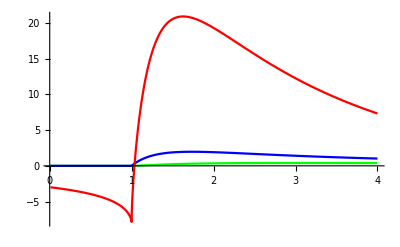

```mathematica
Show[LOImPlot, NLOImPlot, NNLOImPlot]
```

```mathematica
(*Define the function to export data points and their corresponding function values*)
ExportDataPoints[fileName_,array_,func_]:=Module[{dataPairs},
(*Create pairs of data points and function values*)
dataPairs=Table[{array[[i]],func[array[[i]]]},{i,1,Length[array]}];
(*Export the data pairs to a file*)
Export[fileName,dataPairs,"CSV"];]
```

```mathematica
zs = Range[0.01, 4, 0.04];
```

```mathematica
ExportDataPoints["LO_Re.csv", zs, Re[C0[#]]&];
ExportDataPoints["NLO_Re.csv", zs, Re[C1I[#]]&];
ExportDataPoints["NNLO_Re.csv", zs, Re[C2I[#, 5]]&];
ExportDataPoints["LO_Im.csv", zs, Im[C0[#]]&];
ExportDataPoints["NLO_Im.csv", zs, Im[C1I[#]]&];
ExportDataPoints["NNLO_Im.csv", zs, Im[C2I[#, 5]]&];
```

```mathematica
C2I[0.6, 5]
```

6.68643-4.25923 ⅈ

```mathematica
C2I[0.7, 5]
```

8.25633-4.64165 ⅈ